# PP - fit

```mathematica
SetDirectory["D:\\Dropbox\\ExperimentDoc\\O(p,pn)\\DataAnalysis\\ppealstics\\pp_data"]
```

D:\Dropbox\ExperimentDoc\O(p,pn)\DataAnalysis\ppealstics\pp_data

```mathematica
model[x_]:= Exp[-1/2 ((x-μ)/σ)^2] ;
modelBG[x_]:= Exp[-1/2 ((x-μ0)/σ0)^2] ;
modelBG2[x_]:=1+a1 x + a2 x^2;
```

```mathematica
SSR[data1_,data2_,modelBG_,range1_,range2_]:=Sum[(nG1 model[data1[[i,1]]]+nB1 modelBG[data1[[i,1]]]-data1[[i,2]])^2+(nG2 model[data2[[i,1]]]+nB2 modelBG[data2[[i,1]]]-data2[[i,2]])^2,{i,range1,range2}];
```

```mathematica
count[data_,range_]:=Sum[If[range[[2]]>data[[i,1]]>range[[1]],data[[i,2]],0],{i,1,Length[data]}]
```

## L20

```mathematica
LU20=Import["201.dat"];
LD20=Import["301.dat"];
```

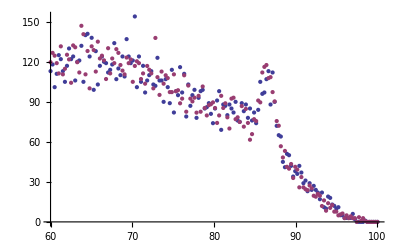

```mathematica
ListPlot[{LU20,LD20}]
```

```mathematica
SSR20=SSR[LU20,LD20,modelBG,81,160];
```

```mathematica
fit20=FindMinimum[SSR20,{{nG1,60},{nG2,60},{μ,86},{σ,1},{nB1,70},{nB2,70},{μ0,81},{σ0,6}}]
```

{4394.45,{nG1→45.0521,nG2→55.6149,μ→86.6384,σ→0.822229,nB1→86.6838,nB2→82.441,μ0→81.4283,σ0→6.51211}}

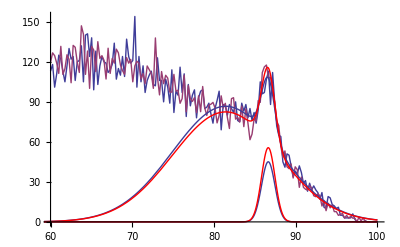

```mathematica
Show[
ListPlot[{LU20,LD20},Joined->True],
Plot[(nG1 model[x]+nB1 modelBG[x])/.fit20[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x]+nB2 modelBG[x])/.fit20[[2]],{x,0,100},PlotRange->All,PlotStyle->Red],
Plot[(nG1 model[x])/.fit20[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit20[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

```mathematica
resLU20=Table[{LU20[[i,1]],LU20[[i,2]]-(nB1 modelBG[LU20[[i,1]]])/.fit20[[2]]},{i,80,140}];
resLD20=Table[{LD20[[i,1]],LD20[[i,2]]-(nB2 modelBG[LD20[[i,1]]])/.fit20[[2]]},{i,80,140}];
range20={μ-2σ,μ+2σ}/.fit[[2]]
```

{84.994,88.2829}

```mathematica
nLU20={count[resLU20,range20],√count[LU20,range20]}
nLD20={count[resLD20,range20],√count[LD20,range20]}
```

{354.598,34.1614}

{437.661,34.7894}

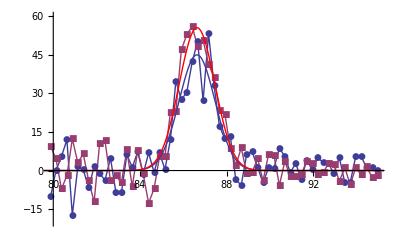

```mathematica
Show[
ListPlot[{resLU20,resLD20},Joined->True,PlotMarkers->Automatic,PlotRange->{-20,60}],
Plot[(nG1 model[x])/.fit[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

## L30

```mathematica
LU30=Import["202.dat"];
LD30=Import["302.dat"];
```

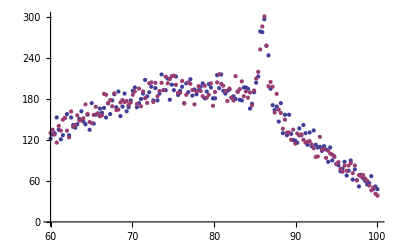

```mathematica
ListPlot[{LU30,LD30}]
```

```mathematica
SSR30=SSR[LU30,LD30,modelBG,70,120];
```

```mathematica
fit30=FindMinimum[SSR30,{{nG1,150},{nG2,150},{μ,86},{σ,1},{nB1,170},{nB2,170},{μ0,80},{σ0,10}}]
```

{13787.5,{nG1→124.121,nG2→117.11,μ→86.0873,σ→0.519507,nB1→194.991,nB2→196.109,μ0→80.6974,σ0→10.1791}}

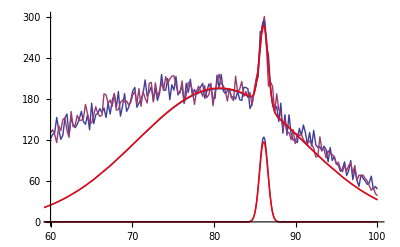

```mathematica
Show[
ListPlot[{LU30,LD30},Joined->True],
Plot[(nG1 model[x]+nB1 modelBG[x])/.fit30[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x]+nB2 modelBG[x])/.fit30[[2]],{x,0,100},PlotRange->All,PlotStyle->Red],
Plot[(nG1 model[x])/.fit30[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit30[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

```mathematica
resLU30=Table[{LU30[[i,1]],LU30[[i,2]]-(nB1 modelBG[LU30[[i,1]]])/.fit30[[2]]},{i,80,140}];
resLD30=Table[{LD30[[i,1]],LD30[[i,2]]-(nB2 modelBG[LD30[[i,1]]])/.fit30[[2]]},{i,80,140}];
range30={μ-2σ,μ+2σ}/.fit30[[2]]
```

{85.0483,87.1264}

```mathematica
nLU30={count[resLU30,range30],√count[LU30,range30]}
nLD30={count[resLD30,range30],√count[LD30,range30]}
```

{610.208,44.3621}

{566.423,43.9545}

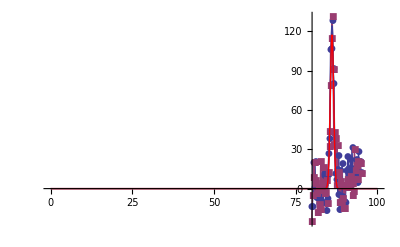

```mathematica
Show[
ListPlot[{resLU30,resLD30},Joined->True,PlotMarkers->Automatic,PlotRange->{-30,All}],
Plot[(nG1 model[x])/.fit30[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit30[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

## L30

```mathematica
LU40=Import["203.dat"];
LD40=Import["303.dat"];
```

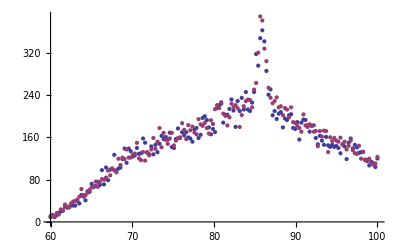

```mathematica
ListPlot[{LU40,LD40}]
```

```mathematica
k=(Solve[{
((b0+b1 x +b2 x^2)/.{x-> 80})==200,
((b0+b1 x +b2 x^2)/.{x-> 90})==200,
((b0+b1 x +b2 x^2)/.{x-> 100})==100},{b0,b1,b2}]//N)[[1]]
```

{b0→-3400.,b1→85.,b2→-0.5}

```mathematica
{b1/b0,b2/b0}/.k
```

{-0.025,0.000147059}

```mathematica
SSR40=SSR[LU40,LD40,modelBG2,50,150];
```

```mathematica
fit40=FindMinimum[SSR40,{{nG1,200},{nG2,200},{μ,86},{σ,1},{nB1,-340},{nB2,-3400},{a1,-0.025},{a2,0.00015}}]
```

{42926.4,{nG1→156.451,nG2→162.445,μ→85.8329,σ→0.561302,nB1→-3342.78,nB2→-3431.12,a1→-0.0251041,a2→0.000148471}}

```mathematica
(√fit40[[1]])/(99-8)
```

2.27678

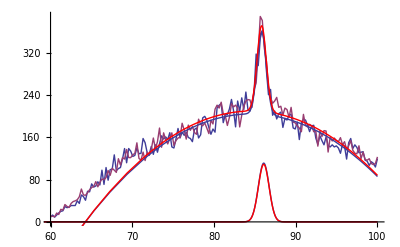

```mathematica
Show[
ListPlot[{LU40,LD40},Joined->True],
Plot[(nG1 model[x]+nB1 modelBG2[x])/.fit40[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x]+nB2 modelBG2[x])/.fit40[[2]],{x,0,100},PlotRange->All,PlotStyle->Red],
Plot[(nG1 model[x])/.fit50[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit50[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

```mathematica
resLU40=Table[{LU40[[i,1]],LU40[[i,2]]-(nB1 modelBG2[LU40[[i,1]]])/.fit40[[2]]},{i,80,140}];
resLD40=Table[{LD40[[i,1]],LD40[[i,2]]-(nB2 modelBG2[LD40[[i,1]]])/.fit40[[2]]},{i,80,140}];
range40={μ-2σ,μ+2σ}/.fit40[[2]]
```

{84.7103,86.9555}

```mathematica
nLU40={count[resLU40,range40],√count[LU40,range40]}
nLD40={count[resLD40,range40],√count[LD40,range40]}
```

{860.564,51.8748}

{848.391,52.2226}

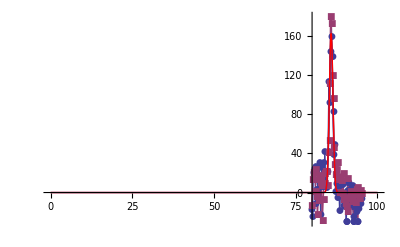

```mathematica
Show[
ListPlot[{resLU40,resLD40},Joined->True,PlotMarkers->Automatic,PlotRange->{-30,All}],
Plot[(nG1 model[x])/.fit40[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit40[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

## L50

```mathematica
LU50=Import["204.dat"];
LD50=Import["304.dat"];
```

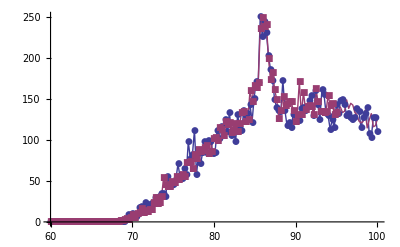

```mathematica
ListPlot[{LU50,LD50},Joined->True,PlotMarkers->Automatic]
```

```mathematica
k=(Solve[{
((b0+b1 x +b2 x^2)/.{x-> 80})==100,
((b0+b1 x +b2 x^2)/.{x-> 90})==150,
((b0+b1 x +b2 x^2)/.{x-> 100})==120},{b0,b1,b2}]//N)[[1]]
```

{b0→-3180.,b1→73.,b2→-0.4}

```mathematica
{b1/b0,b2/b0}/.k
```

{-0.022956,0.000125786}

```mathematica
SSR50=SSR[LU50,LD50,modelBG2,60,160];
```

```mathematica
fit50=FindMinimum[SSR50,{{nG1,100},{nG2,100},{μ,86},{σ,1},{nB1,-3180},{nB2,-3180},{a1,-0.023},{a2,0.0002}}]
```

{25258.7,{nG1→111.367,nG2→109.059,μ→86.0856,σ→0.658961,nB1→-2681.02,nB2→-2750.47,a1→-0.0230574,a2→0.000126272}}

```mathematica
(√fit50[[1]])/(99-8)
```

1.74648

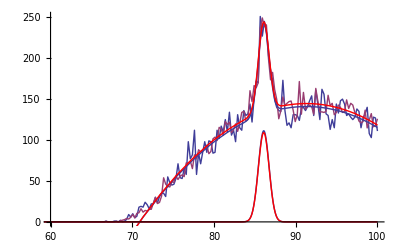

```mathematica
Show[
ListPlot[{LU50,LD50},Joined->True],
Plot[(nG1 model[x]+nB1 modelBG2[x])/.fit50[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x]+nB2 modelBG2[x])/.fit50[[2]],{x,0,100},PlotRange->All,PlotStyle->Red],
Plot[(nG1 model[x])/.fit50[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit50[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

```mathematica
resLU50=Table[{LU50[[i,1]],LU50[[i,2]]-(nB1 modelBG2[LU50[[i,1]]])/.fit50[[2]]},{i,80,140}];
resLD50=Table[{LD50[[i,1]],LD50[[i,2]]-(nB2 modelBG2[LD50[[i,1]]])/.fit50[[2]]},{i,80,140}];
range50={μ-2σ,μ+2σ}/.fit50[[2]]
```

{84.7677,87.4035}

```mathematica
nLU50={count[resLU50,range50],√count[LU50,range50]}
nLD50={count[resLD50,range50],√count[LD50,range50]}
```

{695.067,44.8219}

{673.629,44.9622}

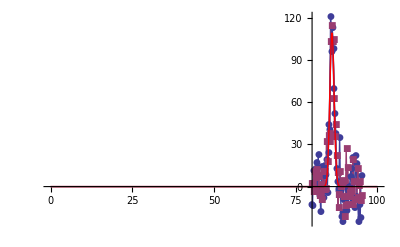

```mathematica
Show[
ListPlot[{resLU50,resLD50},Joined->True,PlotMarkers->Automatic,PlotRange->{-30,All}],
Plot[(nG1 model[x])/.fit50[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit50[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

## L60

```mathematica
LU60=Import["205.dat"];
LD60=Import["305.dat"];
```

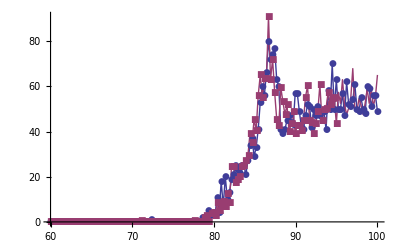

```mathematica
ListPlot[{LU60,LD60},Joined->True,PlotMarkers->Automatic]
```

```mathematica
k=(Solve[{
((b0+b1 x +b2 x^2)/.{x-> 80})==5,
((b0+b1 x +b2 x^2)/.{x-> 90})==40,
((b0+b1 x +b2 x^2)/.{x-> 100})==60},{b0,b1,b2}]//N)[[1]]
```

{b0→-815.,b1→16.25,b2→-0.075}

```mathematica
{b1/b0,b2/b0}/.k
```

{-0.0199387,0.0000920245}

```mathematica
SSR60=SSR[LU60,LD60,modelBG2,80,160];
```

```mathematica
fit60=FindMinimum[SSR60,{{nG1,100},{nG2,100},{μ,86},{σ,1},{nB1,-815},{nB2,-815},{a1,-0.020},{a2,0.00092}}]
```

{5723.9,{nG1→37.2651,nG2→36.9642,μ→86.6336,σ→0.954614,nB1→-1412.31,nB2→-1416.93,a1→-0.0212472,a2→0.000108689}}

```mathematica
(√fit60[[1]])/(81-8)
```

1.03639

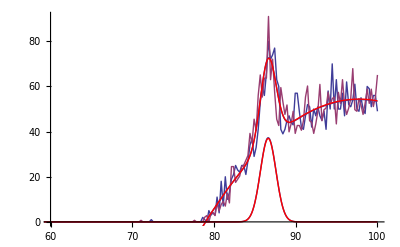

```mathematica
Show[
ListPlot[{LU60,LD60},Joined->True],
Plot[(nG1 model[x]+nB1 modelBG2[x])/.fit60[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x]+nB2 modelBG2[x])/.fit60[[2]],{x,0,100},PlotRange->All,PlotStyle->Red],
Plot[(nG1 model[x])/.fit60[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit60[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

```mathematica
resLU60=Table[{LU60[[i,1]],LU60[[i,2]]-(nB1 modelBG2[LU60[[i,1]]])/.fit60[[2]]},{i,80,140}];
resLD60=Table[{LD60[[i,1]],LD60[[i,2]]-(nB2 modelBG2[LD60[[i,1]]])/.fit60[[2]]},{i,80,140}];
range60={μ-2σ,μ+2σ}/.fit60[[2]]
```

{84.7244,88.5428}

```mathematica
nLU60={count[resLU60,range60],√count[LU60,range60]}
nLD60={count[resLD60,range60],√count[LD60,range60]}
```

{316.083,29.0517}

{344.658,29.5686}

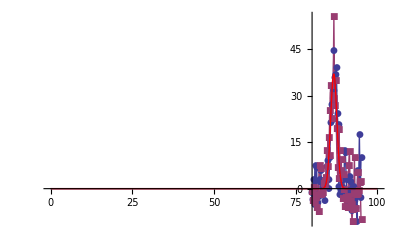

```mathematica
Show[
ListPlot[{resLU60,resLD60},Joined->True,PlotMarkers->Automatic,PlotRange->{-30,All}],
Plot[(nG1 model[x])/.fit60[[2]],{x,0,100},PlotRange->All],
Plot[(nG2 model[x])/.fit60[[2]],{x,0,100},PlotRange->All,PlotStyle->Red]
]
```

## Polarization

```mathematica
P[yU_,yD_,Ay_,α_]:=(-yD+yU)/(2 Ay (yD+yU α))
ΔP[yU_,yD_,ΔyU_,ΔyD_,Ay_,α_]:=((1+α)√(yD^2 ΔyU^2+yU^2 ΔyD^2))/(4 Ay (yD+yU α)^2)
```

```mathematica
P20={P[nLU20[[1]],nLD20[[1]],0.3233,0.78],ΔP[nLU20[[1]],nLD20[[1]],nLU20[[2]],nLD20[[2]],0.3233,0.78]}
P30={P[nLU30[[1]],nLD30[[1]],0.1586,0.78],ΔP[nLU30[[1]],nLD30[[1]],nLU30[[2]],nLD30[[2]],0.1586,0.78]}
P40={P[nLU40[[1]],nLD40[[1]],-0.03654,0.78],ΔP[nLU40[[1]],nLD40[[1]],nLU40[[2]],nLD40[[2]],-0.03654,0.78]}
P50={P[nLU50[[1]],nLD50[[1]],-0.2207,0.78],ΔP[nLU50[[1]],nLD50[[1]],nLU50[[2]],nLD50[[2]],-0.2207,0.78]}
P60={P[nLU60[[1]],nLD60[[1]],-0.3545,0.78],ΔP[nLU60[[1]],nLD60[[1]],nLU60[[2]],nLD60[[2]],-0.3545,0.78]}
```

{-0.179856,0.0522984}

{0.132424,0.0949062}

{-0.109616,-0.331723}

{-0.039949,-0.0592766}

{0.0681712,-0.0491922}

```mathematica
LU={{20,nLU20[[1]]},{30,nLU30[[1]]},{40,nLU40[[1]]},{50,nLU50[[1]]},{60,nLU60[[1]]}};
LD={{20,nLD20[[1]]},{30,nLD30[[1]]},{40,nLD40[[1]]},{50,nLD50[[1]]},{60,nLD60[[1]]}};
```

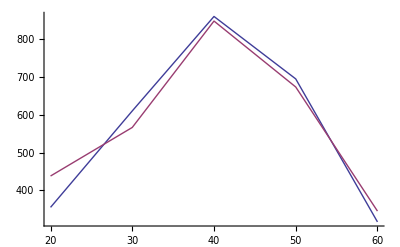

```mathematica
ListPlot[{LU,LD},Joined->True,PlotRange->{{10,70},{0,All}}]
```

```mathematica
p={P20[[1]],P30[[1]],P40[[1]],P50[[1]],P60[[1]]};
Δp={P20[[2]],P30[[2]],P40[[2]],P50[[2]],P60[[2]]};
w=1/Δp^2
```

{365.615,111.023,9.08761,284.599,413.245}

```mathematica
wp=p w
```

{-65.7578,14.7021,-0.996143,-11.3694,28.1714}

```mathematica
Total[wp]/Total[w]
```

-0.0297828

```mathematica
√(1/Total[w])
```

0.0290672

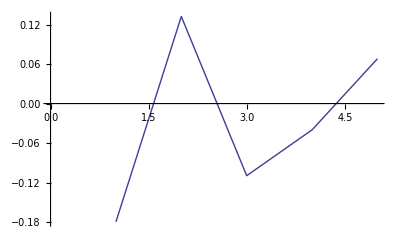

```mathematica
ListPlot[p,Joined->True]
```